# Mosquito population dynamics include Early instars, layter instars, pupae, and adults female.

## How to use

Using the code here we can determine seasonal patterns in infection and test the effect of IRS on the mosquito populations. This is a deterministic implementation of the model by White et al. 2011, which itself relies on other references and particularly Griffin et al. 2010. The workflow is to feed the function here the seasonal and/or IRS scheme that we want, and to take the output and feed it to the parameter file of the ABM.

White MT, Griffin JT, Churcher TS, Ferguson NM, Basáñez M-G, Ghani AC. Modelling the impact of vector control interventions on Anopheles gambiae population dynamics. Parasit Vectors. 2011;4: 153.

```mathematica
ClearAll[A,P,L,M,K,f,MuM,MuE,MuL, c, TimeMax];
```

## Carrying capacity

(* 
Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity. It is just a sinus function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. What is different between the Seasonality sub-sections below is the values of FirstDayOfRain, LastDayOfRain, the multipliers of the sinus function and the baseline number of mosquitoes
*)

```mathematica
Seasonality 1
```

```mathematica
FirstDayOfRain=160; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.5;
Muliplier2=0.5;
BaseLine=100;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 2
```

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.5;
Muliplier2=0.5;
BaseLine=100;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 3
```

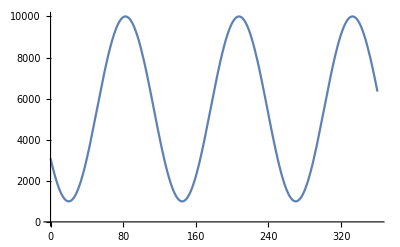

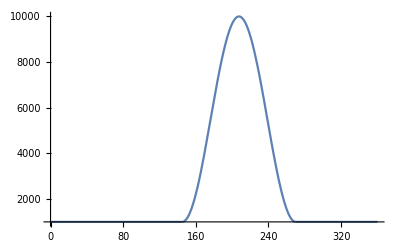

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.55;
Muliplier2=0.45;
BaseLine=1000;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 4 (used for the PLOS Biol paper)
```

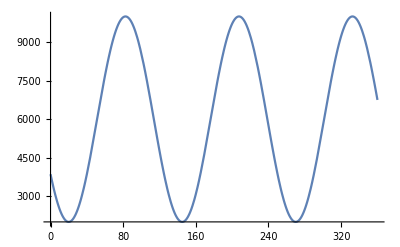

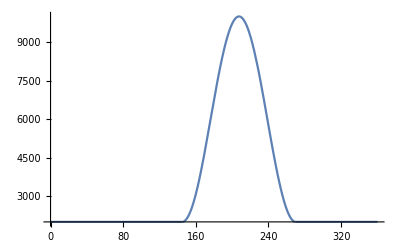

```mathematica
FirstDayOfRain=145; (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270;(* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
Muliplier1=0.6;
Muliplier2=0.4;
BaseLine=2000;
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(Muliplier1+Muliplier2*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0.5 and the addition of 0.5 is to define a minimum (positive) and a maximum value for the number of mosquitos. The 10000 is just an arbitrary number. *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},BaseLine];  (*Seasonality in carrying capacity. In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

## Mortality rates

### Non - adult mortality rates

(* 
MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages, respectively.  Both are density-dependent on the number of early and late larva stages, calculated as (A+L)/f, where f is the environmental carrying capacity at time t; 
\mu_E^0 and \mu_L^0 are assumed to be 0.035 and γ = 13.25. These values are taken from Table 1 in White et al 2011. The equations are Eq. 7 in the paper.
*)

```mathematica
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

### Adult mortality rates -- this is the definition of the intervention

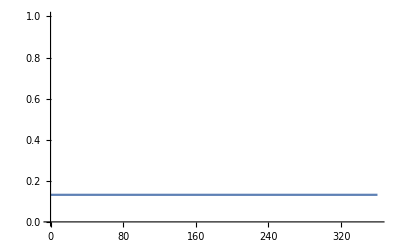

0.9

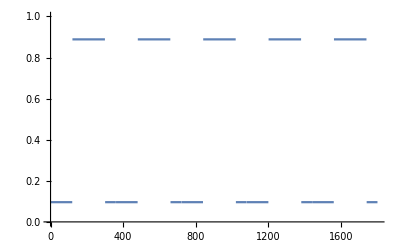

```mathematica
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)

(*MuM is the daily mortality rate of adult mosquitos.The Log turns the w into a rate.*)

(* Example 0: No external mortality rates (no IRS), so c=0 *)
c=0;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= {-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,0<t<TimeMax};
Plot[Evaluate[MuM[0,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]

(* Example 1: IRS of 3 months, May-July, with c=0.9, for 5 years *)
c=0.9
TimeMax=5*360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,120<Mod[t,360]<300}},MuM0];
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]
(* Plot the mortality rates *)
```

## Mosquito population dynamics without IRS (only seasonality). Used for PLOS Biology

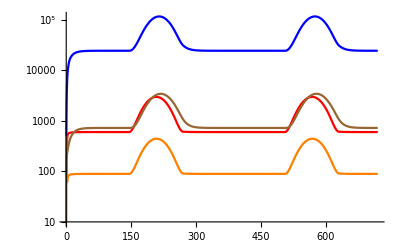

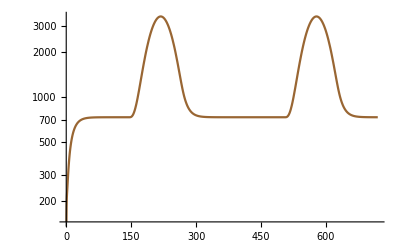

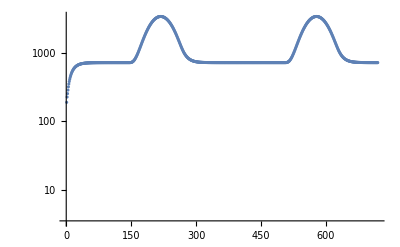

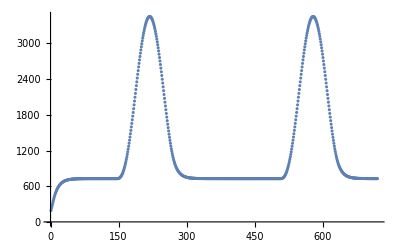

```mathematica
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)

TimeMax=720;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoNoIRS,2]};
data=Delete[data,1];
ListLogPlot[data, PlotRange->{0,Max[data]+1}]
ListPlot[data, PlotRange->{0,Max[data]+1}]
(*Export["~/Documents/malaria_interventions/mosquito_population_plosbiol_4.csv",data[[361;;720]]];*)
```

```mathematica
(*Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.*)
```

```mathematica
data[[361;;720]]
```

## IRS SCHEME OF GHANA FIELD DATA (Used For PLOS Biology)

(*

The MuM function mimics the IRS applied in the field. IRS 1 had a coverage of 80%, IRS 2+3 had a coverage of 96%. To include the effect of the lifetime of the insecticides, and the fact that it takes time to spray all the compounds, we set the start time of the intervention to the middle time of the length it took to spray, and the total length of the intervention to the half-life of the insecticide. Specifically: 

IRS 1: Done between Oct-Dec 2013; We set starting date to Nov. 1st (running day 661). The intervention was with Organophosphates with lifetime of 2-3m. So we set the length to 75 days (661-735)
IRS 2: Done between May-Jul 2013; We set starting date to June 1st (running day 871). The intervention was with Organophosphates with lifetime of 2-3m. So we set the length to 75 days (871-945)
IRS 3: Done between Dec-Feb 2014; We set starting date to Jan 1st (running day 1081). The intervention was with 721+360 with lifetime of 4-6m. So we set the length to 150 days (1081-1230).

We let the model run for 5 years, to capture any effects of IRS on S5 and S6. We take the IRS data from day 661 because it takes one cycle (a year) to initiate the correct values (just like with the model without IRS, just seasonality)

*)

1800

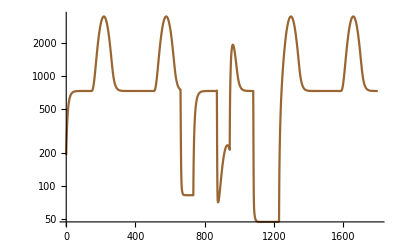

{{661,747.752},{662,422.136},{663,259.833},{664,178.387},{665,136.965},{666,115.381},{667,103.679},{668,96.9635},{669,92.8359},{670,90.1163},{671,88.2166},{672,86.8327},{673,85.7976},{674,85.0116},{675,84.4099},{676,83.9475},{677,83.5916},{678,83.3173},{679,83.106},{680,82.9431},{681,82.8176},{682,82.7209},{683,82.6463},{684,82.5888},{685,82.5446},{686,82.5104},{687,82.4841},{688,82.4639},{689,82.4482},{690,82.4362},{691,82.4269},{692,82.4198},{693,82.4143},{694,82.41},{695,82.4067},{696,82.4042},{697,82.4023},{698,82.4008},{699,82.3996},{700,82.3987},{701,82.398},{702,82.3975},{703,82.3971},{704,82.3968},{705,82.3966},{706,82.3964},{707,82.3962},{708,82.3961},{709,82.396},{710,82.396},{711,82.3959},{712,82.3959},{713,82.3958},{714,82.3958},{715,82.3958},{716,82.3958},{717,82.3958},{718,82.3958},{719,82.3958},{720,82.3958},{721,82.3958},{722,82.3958},{723,82.3958},{724,82.3957},{725,82.3957},{726,82.3957},{727,82.3957},{728,82.3957},{729,82.3957},{730,82.3957},{731,82.3957},{732,82.3957},{733,82.3957},{734,82.3957},{735,82.3957},{736,129.767},{737,173.308},{738,214.205},{739,253.102},{740,290.07},{741,324.972},{742,357.679},{743,388.145},{744,416.391},{745,442.492},{746,466.549},{747,488.681},{748,509.015},{749,527.675},{750,544.786},{751,560.465},{752,574.825},{753,587.97},{754,599.999},{755,611.003},{756,621.067},{757,630.269},{758,638.681},{759,646.37},{760,653.397},{761,659.817},{762,665.684},{763,671.043},{764,675.939},{765,680.41},{766,684.494},{767,688.224},{768,691.631},{769,694.741},{770,697.582},{771,700.175},{772,702.544},{773,704.706},{774,706.68},{775,708.482},{776,710.128},{777,711.63},{778,713.001},{779,714.253},{780,715.396},{781,716.44},{782,717.392},{783,718.262},{784,719.055},{785,719.78},{786,720.441},{787,721.045},{788,721.596},{789,722.099},{790,722.558},{791,722.977},{792,723.359},{793,723.709},{794,724.027},{795,724.318},{796,724.584},{797,724.826},{798,725.047},{799,725.249},{800,725.434},{801,725.602},{802,725.755},{803,725.896},{804,726.023},{805,726.14},{806,726.247},{807,726.344},{808,726.433},{809,726.514},{810,726.588},{811,726.655},{812,726.717},{813,726.773},{814,726.825},{815,726.872},{816,726.914},{817,726.953},{818,726.989},{819,727.022},{820,727.051},{821,727.078},{822,727.103},{823,727.126},{824,727.146},{825,727.165},{826,727.182},{827,727.198},{828,727.212},{829,727.225},{830,727.237},{831,727.248},{832,727.258},{833,727.267},{834,727.275},{835,727.283},{836,727.29},{837,727.296},{838,727.302},{839,727.307},{840,727.312},{841,727.316},{842,727.32},{843,727.324},{844,727.327},{845,727.33},{846,727.333},{847,727.335},{848,727.338},{849,727.34},{850,727.342},{851,727.343},{852,727.345},{853,727.346},{854,727.348},{855,727.349},{856,727.35},{857,727.351},{858,727.352},{859,727.353},{860,727.354},{861,727.354},{862,727.355},{863,727.356},{864,727.356},{865,727.357},{866,727.368},{867,727.523},{868,728.083},{869,729.322},{870,731.494},{871,734.827},{872,291.899},{873,144.293},{874,95.124},{875,78.7046},{876,73.2104},{877,71.4519},{878,71.1005},{879,71.4214},{880,72.1876},{881,73.3253},{882,74.8024},{883,76.5964},{884,78.6868},{885,81.0534},{886,83.6769},{887,86.5391},{888,89.6226},{889,92.9109},{890,96.3882},{891,100.039},{892,103.85},{893,107.804},{894,111.889},{895,116.089},{896,120.39},{897,124.778},{898,129.239},{899,133.757},{900,138.319},{901,142.911},{902,147.518},{903,152.126},{904,156.722},{905,161.291},{906,165.819},{907,170.295},{908,174.704},{909,179.033},{910,183.271},{911,187.406},{912,191.425},{913,195.317},{914,199.072},{915,202.678},{916,206.127},{917,209.409},{918,212.514},{919,215.435},{920,218.163},{921,220.691},{922,223.013},{923,225.122},{924,227.012},{925,228.679},{926,230.118},{927,231.326},{928,232.299},{929,233.034},{930,233.53},{931,233.786},{932,233.801},{933,233.574},{934,233.107},{935,232.4},{936,231.456},{937,230.277},{938,228.866},{939,227.226},{940,225.363},{941,223.28},{942,220.984},{943,218.48},{944,215.774},{945,212.875},{946,411.134},{947,590.749},{948,758.451},{949,917.436},{950,1066.96},{951,1205.05},{952,1330.24},{953,1441.84},{954,1539.83},{955,1624.57},{956,1696.67},{957,1756.84},{958,1805.88},{959,1844.55},{960,1873.66},{961,1893.95},{962,1906.16},{963,1911.},{964,1909.12},{965,1901.15},{966,1887.69},{967,1869.31},{968,1846.55},{969,1819.9},{970,1789.85},{971,1756.86},{972,1721.34},{973,1683.72},{974,1644.36},{975,1603.65},{976,1561.91},{977,1519.49},{978,1476.69},{979,1433.81},{980,1391.12},{981,1348.88},{982,1307.35},{983,1266.76},{984,1227.32},{985,1189.25},{986,1152.73},{987,1117.95},{988,1085.07},{989,1054.25},{990,1025.63},{991,999.327},{992,975.315},{993,953.432},{994,933.494},{995,915.327},{996,898.772},{997,883.685},{998,869.935},{999,857.401},{1000,845.976},{1001,835.559},{1002,826.062},{1003,817.403},{1004,809.506},{1005,802.305},{1006,795.738},{1007,789.748},{1008,784.284},{1009,779.3},{1010,774.754},{1011,770.607},{1012,766.824},{1013,763.372},{1014,760.223},{1015,757.35},{1016,754.728},{1017,752.336},{1018,750.154},{1019,748.162},{1020,746.345},{1021,744.686},{1022,743.173},{1023,741.792},{1024,740.531},{1025,739.381},{1026,738.332},{1027,737.374},{1028,736.499},{1029,735.702},{1030,734.974},{1031,734.309},{1032,733.702},{1033,733.149},{1034,732.644},{1035,732.183},{1036,731.762},{1037,731.378},{1038,731.027},{1039,730.707},{1040,730.415},{1041,730.149},{1042,729.906},{1043,729.684},{1044,729.481},{1045,729.296},{1046,729.127},{1047,728.973},{1048,728.832},{1049,728.704},{1050,728.587},{1051,728.48},{1052,728.382},{1053,728.293},{1054,728.212},{1055,728.138},{1056,728.07},{1057,728.008},{1058,727.952},{1059,727.9},{1060,727.853},{1061,727.81},{1062,727.771},{1063,727.736},{1064,727.703},{1065,727.673},{1066,727.646},{1067,727.621},{1068,727.599},{1069,727.578},{1070,727.559},{1071,727.542},{1072,727.526},{1073,727.512},{1074,727.499},{1075,727.487},{1076,727.476},{1077,727.466},{1078,727.457},{1079,727.448},{1080,727.441},{1081,727.434},{1082,285.908},{1083,137.612},{1084,87.0438},{1085,68.9855},{1086,61.7609},{1087,58.2124},{1088,56.0011},{1089,54.3687},{1090,53.0644},{1091,51.9948},{1092,51.1135},{1093,50.3889},{1094,49.7949},{1095,49.3092},{1096,48.9129},{1097,48.5899},{1098,48.3269},{1099,48.1129},{1100,47.9387},{1101,47.797},{1102,47.6818},{1103,47.5881},{1104,47.5119},{1105,47.4499},{1106,47.3995},{1107,47.3585},{1108,47.3251},{1109,47.298},{1110,47.276},{1111,47.258},{1112,47.2435},{1113,47.2316},{1114,47.222},{1115,47.2141},{1116,47.2077},{1117,47.2025},{1118,47.1983},{1119,47.1949},{1120,47.1921},{1121,47.1898},{1122,47.188},{1123,47.1865},{1124,47.1853},{1125,47.1843},{1126,47.1835},{1127,47.1828},{1128,47.1823},{1129,47.1818},{1130,47.1815},{1131,47.1812},{1132,47.181},{1133,47.1808},{1134,47.1806},{1135,47.1805},{1136,47.1804},{1137,47.1803},{1138,47.1802},{1139,47.1802},{1140,47.1801},{1141,47.1801},{1142,47.1801},{1143,47.1801},{1144,47.18},{1145,47.18},{1146,47.18},{1147,47.18},{1148,47.18},{1149,47.18},{1150,47.18},{1151,47.18},{1152,47.18},{1153,47.18},{1154,47.18},{1155,47.18},{1156,47.18},{1157,47.18},{1158,47.18},{1159,47.18},{1160,47.18},{1161,47.1799},{1162,47.1799},{1163,47.1799},{1164,47.1799},{1165,47.1799},{1166,47.1799},{1167,47.1799},{1168,47.1799},{1169,47.1799},{1170,47.1799},{1171,47.1799},{1172,47.1799},{1173,47.1799},{1174,47.1799},{1175,47.1799},{1176,47.1799},{1177,47.1799},{1178,47.1799},{1179,47.1799},{1180,47.1799},{1181,47.1799},{1182,47.1799},{1183,47.1799},{1184,47.1799},{1185,47.1799},{1186,47.1799},{1187,47.1799},{1188,47.1799},{1189,47.1799},{1190,47.1799},{1191,47.1799},{1192,47.1799},{1193,47.1799},{1194,47.1799},{1195,47.1799},{1196,47.1799},{1197,47.1799},{1198,47.1799},{1199,47.1799},{1200,47.1799},{1201,47.1799},{1202,47.1799},{1203,47.1799},{1204,47.1799},{1205,47.1799},{1206,47.1799},{1207,47.1799},{1208,47.1799},{1209,47.1799},{1210,47.1799},{1211,47.1799},{1212,47.1799},{1213,47.1799},{1214,47.1799},{1215,47.1799},{1216,47.1799},{1217,47.1799},{1218,47.1799},{1219,47.1799},{1220,47.1799},{1221,47.1799},{1222,47.1799},{1223,47.1799},{1224,47.1799},{1225,47.1799},{1226,47.1819},{1227,47.215},{1228,47.3362},{1229,47.5909},{1230,48.0047},{1231,94.6062},{1232,138.664},{1233,182.28},{1234,226.836},{1235,272.604},{1236,319.312},{1237,366.635},{1238,414.367},{1239,462.427},{1240,510.825},{1241,559.622},{1242,608.912},{1243,658.797},{1244,709.382},{1245,760.767},{1246,813.038},{1247,866.27},{1248,920.526},{1249,975.849},{1250,1032.27},{1251,1089.81},{1252,1148.46},{1253,1208.21},{1254,1269.04},{1255,1330.91},{1256,1393.77},{1257,1457.56},{1258,1522.2},{1259,1587.61},{1260,1653.71},{1261,1720.39},{1262,1787.56},{1263,1855.09},{1264,1922.88},{1265,1990.79},{1266,2058.7},{1267,2126.48},{1268,2193.99},{1269,2261.1},{1270,2327.67},{1271,2393.55},{1272,2458.61},{1273,2522.7},{1274,2585.68},{1275,2647.41},{1276,2707.76},{1277,2766.58},{1278,2823.74},{1279,2879.11},{1280,2932.57},{1281,2983.97},{1282,3033.22},{1283,3080.18},{1284,3124.75},{1285,3166.83},{1286,3206.3},{1287,3243.09},{1288,3277.1},{1289,3308.25},{1290,3336.46},{1291,3361.67},{1292,3383.82},{1293,3402.85},{1294,3418.73},{1295,3431.4},{1296,3440.85},{1297,3447.06},{1298,3449.99},{1299,3449.66},{1300,3446.07},{1301,3439.22},{1302,3429.14},{1303,3415.84},{1304,3399.38},{1305,3379.78},{1306,3357.1},{1307,3331.4},{1308,3302.75},{1309,3271.22},{1310,3236.88},{1311,3199.84},{1312,3160.17},{1313,3117.99},{1314,3073.4},{1315,3026.52},{1316,2977.46},{1317,2926.35},{1318,2873.33},{1319,2818.52},{1320,2762.07},{1321,2704.12},{1322,2644.82},{1323,2584.32},{1324,2522.78},{1325,2460.35},{1326,2397.19},{1327,2333.47},{1328,2269.35},{1329,2204.99},{1330,2140.55},{1331,2076.22},{1332,2012.13},{1333,1948.48},{1334,1885.41},{1335,1823.09},{1336,1761.67},{1337,1701.33},{1338,1642.21},{1339,1584.46},{1340,1528.24},{1341,1473.69},{1342,1420.95},{1343,1370.15},{1344,1321.43},{1345,1274.9},{1346,1230.7},{1347,1188.93},{1348,1149.69},{1349,1113.08},{1350,1079.2},{1351,1048.11},{1352,1019.75},{1353,993.904},{1354,970.364},{1355,948.919},{1356,929.382},{1357,911.58},{1358,895.357},{1359,880.573},{1360,867.098},{1361,854.816},{1362,843.619},{1363,833.41},{1364,824.103},{1365,815.616},{1366,807.877},{1367,800.819},{1368,794.382},{1369,788.511},{1370,783.156},{1371,778.272},{1372,773.816},{1373,769.751},{1374,766.043},{1375,762.66},{1376,759.573},{1377,756.757},{1378,754.187},{1379,751.842},{1380,749.703},{1381,747.751},{1382,745.969},{1383,744.344},{1384,742.86},{1385,741.507},{1386,740.271},{1387,739.144},{1388,738.115},{1389,737.176},{1390,736.319},{1391,735.537},{1392,734.823},{1393,734.172},{1394,733.577},{1395,733.035},{1396,732.539},{1397,732.087},{1398,731.675},{1399,731.298},{1400,730.955},{1401,730.641},{1402,730.355},{1403,730.094},{1404,729.855},{1405,729.638},{1406,729.439},{1407,729.258},{1408,729.092},{1409,728.941},{1410,728.803},{1411,728.678},{1412,728.563},{1413,728.458},{1414,728.362},{1415,728.275},{1416,728.195},{1417,728.123},{1418,728.056},{1419,727.996},{1420,727.94},{1421,727.89},{1422,727.844},{1423,727.802},{1424,727.763},{1425,727.728},{1426,727.696},{1427,727.667},{1428,727.64},{1429,727.616},{1430,727.594},{1431,727.574},{1432,727.555},{1433,727.538},{1434,727.523},{1435,727.509},{1436,727.496},{1437,727.484},{1438,727.474},{1439,727.464},{1440,727.455},{1441,727.447},{1442,727.439},{1443,727.433},{1444,727.426},{1445,727.421},{1446,727.416},{1447,727.411},{1448,727.407},{1449,727.403},{1450,727.399},{1451,727.396},{1452,727.393},{1453,727.39},{1454,727.388},{1455,727.385},{1456,727.383},{1457,727.381},{1458,727.38},{1459,727.378},{1460,727.377},{1461,727.375},{1462,727.374},{1463,727.373},{1464,727.372},{1465,727.371},{1466,727.37},{1467,727.37},{1468,727.369},{1469,727.368},{1470,727.368},{1471,727.367},{1472,727.367},{1473,727.366},{1474,727.366},{1475,727.366},{1476,727.365},{1477,727.365},{1478,727.365},{1479,727.364},{1480,727.364},{1481,727.364},{1482,727.364},{1483,727.364},{1484,727.363},{1485,727.363},{1486,727.363},{1487,727.363},{1488,727.363},{1489,727.363},{1490,727.363},{1491,727.363},{1492,727.363},{1493,727.362},{1494,727.362},{1495,727.362},{1496,727.362},{1497,727.362},{1498,727.362},{1499,727.362},{1500,727.362},{1501,727.362},{1502,727.362},{1503,727.362},{1504,727.362},{1505,727.362},{1506,727.362},{1507,727.362},{1508,727.362},{1509,727.362},{1510,727.362},{1511,727.362},{1512,727.362},{1513,727.362},{1514,727.362},{1515,727.362},{1516,727.362},{1517,727.362},{1518,727.362},{1519,727.362},{1520,727.362},{1521,727.362},{1522,727.362},{1523,727.362},{1524,727.362},{1525,727.362},{1526,727.362},{1527,727.362},{1528,727.362},{1529,727.362},{1530,727.362},{1531,727.362},{1532,727.362},{1533,727.362},{1534,727.362},{1535,727.362},{1536,727.362},{1537,727.362},{1538,727.362},{1539,727.362},{1540,727.362},{1541,727.362},{1542,727.362},{1543,727.362},{1544,727.362},{1545,727.362},{1546,727.362},{1547,727.362},{1548,727.362},{1549,727.362},{1550,727.362},{1551,727.362},{1552,727.362},{1553,727.362},{1554,727.362},{1555,727.362},{1556,727.362},{1557,727.362},{1558,727.362},{1559,727.362},{1560,727.362},{1561,727.362},{1562,727.362},{1563,727.362},{1564,727.362},{1565,727.362},{1566,727.362},{1567,727.362},{1568,727.362},{1569,727.362},{1570,727.362},{1571,727.362},{1572,727.362},{1573,727.362},{1574,727.362},{1575,727.362},{1576,727.362},{1577,727.362},{1578,727.362},{1579,727.362},{1580,727.362},{1581,727.362},{1582,727.362},{1583,727.362},{1584,727.362},{1585,727.362},{1586,727.372},{1587,727.527},{1588,728.086},{1589,729.325},{1590,731.497},{1591,734.83},{1592,739.531},{1593,745.78},{1594,753.737},{1595,763.543},{1596,775.318},{1597,789.165},{1598,805.169},{1599,823.403},{1600,843.92},{1601,866.764},{1602,891.963},{1603,919.533},{1604,949.479},{1605,981.795},{1606,1016.46},{1607,1053.45},{1608,1092.73},{1609,1134.24},{1610,1177.94},{1611,1223.74},{1612,1271.59},{1613,1321.39},{1614,1373.05},{1615,1426.47},{1616,1481.56},{1617,1538.19},{1618,1596.24},{1619,1655.59},{1620,1716.11},{1621,1777.66},{1622,1840.11},{1623,1903.3},{1624,1967.1},{1625,2031.34},{1626,2095.88},{1627,2160.56},{1628,2225.23},{1629,2289.73},{1630,2353.9},{1631,2417.58},{1632,2480.62},{1633,2542.85},{1634,2604.13},{1635,2664.31},{1636,2723.22},{1637,2780.73},{1638,2836.69},{1639,2890.96},{1640,2943.4},{1641,2993.89},{1642,3042.28},{1643,3088.47},{1644,3132.33},{1645,3173.75},{1646,3212.64},{1647,3248.88},{1648,3282.39},{1649,3313.08},{1650,3340.87},{1651,3365.7},{1652,3387.5},{1653,3406.22},{1654,3421.8},{1655,3434.21},{1656,3443.41},{1657,3449.39},{1658,3452.13},{1659,3451.61},{1660,3447.85},{1661,3440.84},{1662,3430.61},{1663,3417.19},{1664,3400.61},{1665,3380.9},{1666,3358.13},{1667,3332.34},{1668,3303.6},{1669,3271.99},{1670,3237.59},{1671,3200.48},{1672,3160.76},{1673,3118.53},{1674,3073.89},{1675,3026.96},{1676,2977.87},{1677,2926.72},{1678,2873.66},{1679,2818.83},{1680,2762.35},{1681,2704.37},{1682,2645.05},{1683,2584.53},{1684,2522.97},{1685,2460.52},{1686,2397.35},{1687,2333.62},{1688,2269.48},{1689,2205.11},{1690,2140.67},{1691,2076.32},{1692,2012.23},{1693,1948.56},{1694,1885.48},{1695,1823.15},{1696,1761.74},{1697,1701.39},{1698,1642.26},{1699,1584.51},{1700,1528.29},{1701,1473.73},{1702,1420.98},{1703,1370.18},{1704,1321.46},{1705,1274.93},{1706,1230.73},{1707,1188.95},{1708,1149.71},{1709,1113.1},{1710,1079.22},{1711,1048.13},{1712,1019.76},{1713,993.917},{1714,970.376},{1715,948.93},{1716,929.392},{1717,911.589},{1718,895.366},{1719,880.581},{1720,867.105},{1721,854.822},{1722,843.624},{1723,833.415},{1724,824.108},{1725,815.62},{1726,807.881},{1727,800.823},{1728,794.385},{1729,788.514},{1730,783.159},{1731,778.274},{1732,773.818},{1733,769.753},{1734,766.045},{1735,762.661},{1736,759.575},{1737,756.758},{1738,754.188},{1739,751.844},{1740,749.704},{1741,747.752},{1742,745.97},{1743,744.345},{1744,742.861},{1745,741.507},{1746,740.272},{1747,739.144},{1748,738.115},{1749,737.176},{1750,736.319},{1751,735.537},{1752,734.824},{1753,734.172},{1754,733.578},{1755,733.035},{1756,732.54},{1757,732.088},{1758,731.675},{1759,731.299},{1760,730.955},{1761,730.641},{1762,730.355},{1763,730.094},{1764,729.855},{1765,729.638},{1766,729.439},{1767,729.258},{1768,729.092},{1769,728.941},{1770,728.803},{1771,728.678},{1772,728.563},{1773,728.458},{1774,728.362},{1775,728.275},{1776,728.195},{1777,728.123},{1778,728.056},{1779,727.996},{1780,727.94},{1781,727.89},{1782,727.844},{1783,727.802},{1784,727.763},{1785,727.728},{1786,727.696},{1787,727.667},{1788,727.64},{1789,727.616},{1790,727.594},{1791,727.574},{1792,727.555},{1793,727.538},{1794,727.523},{1795,727.509},{1796,727.496},{1797,727.484},{1798,727.474},{1799,727.464},{1800,727.455}}

~/Documents/malaria_interventions/IRS_Ghana.csv

```mathematica
MuM [c1_,c2_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c1,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,301+360<=t<=375+360},{-Log[0.91*w[c2,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,511+360<=t≤585+360||721+360<=t<=870+360}},MuM0]; 
(*Table[MuM[0.8,0.96,0.92,0.97,0.207,0.86,t],{t,1,1440}]*)
TimeMax=5*360;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[0.8,0.96,0.92,0.97,0.207,0.86,t]*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,1,TimeMax}];
(*LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *) *)

MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,1,TimeMax}];
data=Transpose@{Range[1,TimeMax],Flatten[MosquitoIRS,2]};
Length[data]
LogPlot[Evaluate[{M[t]}/.sol],{t,1,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
data[[661;;TimeMax]]
Export["~/Documents/malaria_interventions/IRS_Ghana.csv",data[[661;;TimeMax]]]
```

## Mosquito population dynamics with IRS

```mathematica
(* Need to set the IRS scheme, so change these next three lines as necessary, see the examples above *)
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)
FirstDay=120;
LastDay=300;
TimeMax=2*360;
c=0.9;

generateIRS[FirstDay_, LastDay_, TimeMax_, coverage_] := {

filename="~/Documents/malaria_interventions_data/IRS_"<>ToString[FirstDay]<>"_"<>ToString[LastDay]<>"_"<>ToString[coverage]<>"_"<>ToString[TimeMax]<>".csv";
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,FirstDay<Mod[t,360]<LastDay}},MuM0];

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
     dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[coverage,0.92,0.97,0.207,0.86,t]*M[t], (*Adult mosquitos, half of them are female*)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown}]; (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}]; (* Plot abundance of adults *)
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];(* Obtain mosquito abundance with intervention*)

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoIRS,2]};
data=Delete[data,1];
Export[filename,data];
data
}
```

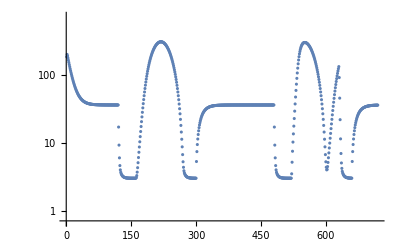

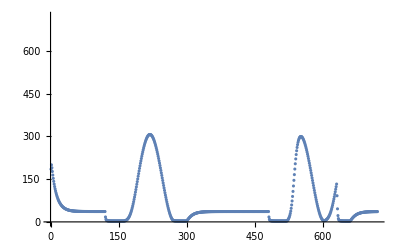

```mathematica
d=generateIRS[120,300,2*360,0.9];
ListLogPlot[d, PlotRange->{0,Max[d]+1}]
ListPlot[d, PlotRange->{0,Max[d]+1}]
```

```mathematica
LengthRange=360*Range[5,20,5];
CoverageRange=Range[0.8,1,0.05];
Table[generateIRS[120,300,a,b],{a,LengthRange},{b,CoverageRange}];
```

```mathematica
5
```